```mathematica
fmu[x_]:=1
fmd[x_] := -1
fd[x_] := Sign[x]
```

```mathematica
fc[x_] := -1 * Sign[x]
```

```mathematica
31-x
```

```mathematica
fmu[3]
```

-27

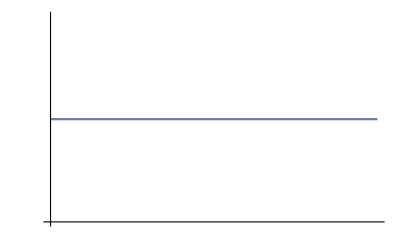

```mathematica
Plot[fmu[x],{x,0,60},PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]]
```

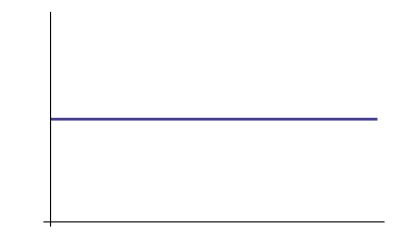

```mathematica
Plot[fmu[x],{x,0,60},PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[2.]],PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]]
```

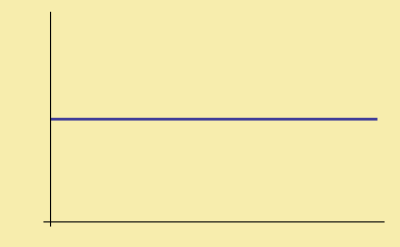

```mathematica
Show[%47,Background->RGBColor[0.97,0.93,0.68]]
```

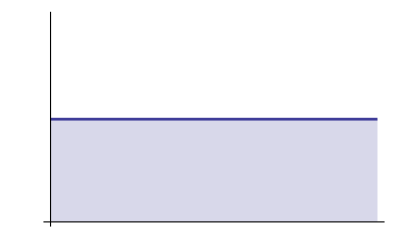

```mathematica
Plot[fmu[x],{x,0,60},Filling->Automatic,PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[2.]],PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]]
```

```mathematica
Show[%47,Background->White]
```

-Graphics-

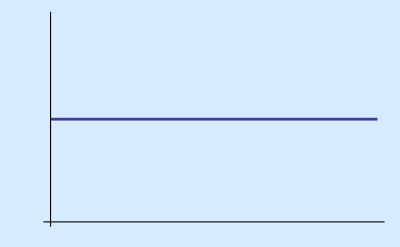

```mathematica
Show[%47,Background->RGBColor[0.84,0.92,1.]]
```

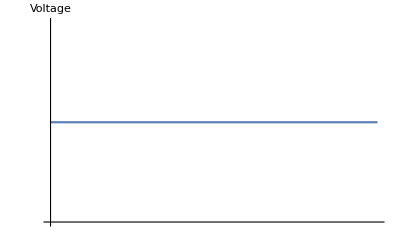

```mathematica
Show[%45,AxesLabel->{None,HoldForm[Voltage]},PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",10,GrayLevel[0]}]
```

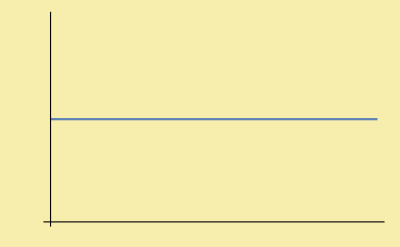

```mathematica
Show[monup,Axes->True,AxesStyle->Black,Background->RGBColor[0.97,0.93,0.68]]
```

```mathematica
diverg= Plot[fd[x],{x,-30,30},PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];
converg  = Plot[fc[x],{x,-30,30},PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];
```

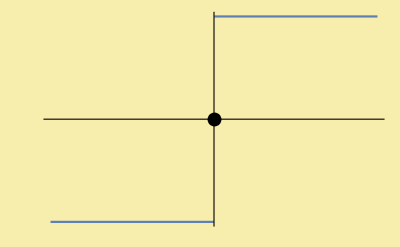

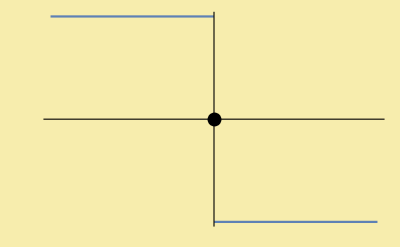

```mathematica
Show[diverg, Graphics[{PointSize[0.025],Point[{0,0}]}],Background->RGBColor[0.97,0.93,0.68]]
Show[converg, Graphics[{PointSize[0.025],Point[{0,0}]}],Background->RGBColor[0.97,0.93,0.68]]
```

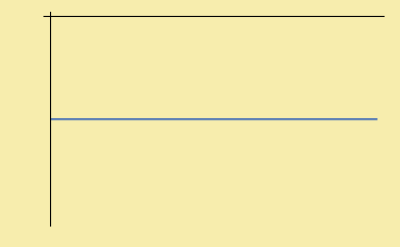

```mathematica
Plot[fmd[x],{x,0,60},PlotTheme->"Minimal",FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],Background->RGBColor[0.97,0.93,0.68]]
```